# Ph 20 Lab 5 (Evaluation -> Evaluate Notebook)

## Part 1

2. Explore functionality of Mathematica

Fourier transform of circular disk (related to diffraction pattern):

(2 π BesselJ[1,k])/k

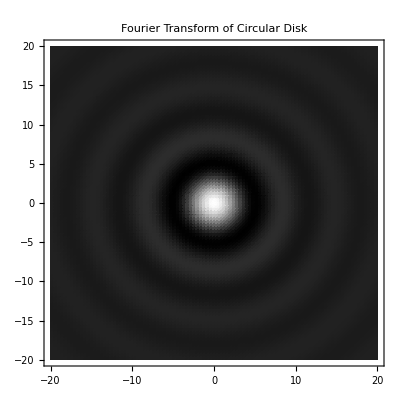

```mathematica
a=20;
thing=Integrate[r Exp[-I k r Cos[θ]],{r,0,1},{θ,0,2π},Assumptions->k>0]
DensityPlot[thing/.k->√(x^2+y^2),{x,-a,a},{y,-a,a},PlotPoints->100,ColorFunction->GrayLevel,PlotRange->Full,PlotLabel->"Fourier Transform of Circular Disk"]
```

## Part 2

1.

0. | 0.
1. | -0.00813765
2. | -0.242631
3. | -1.64112
4. | -5.90986
5. | -14.8744

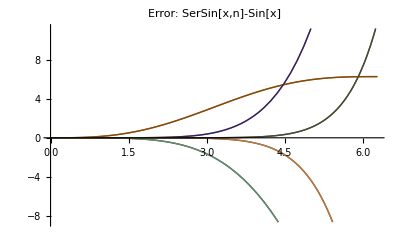

```mathematica
SerCos[x_,n_]:=Normal[Series[Cos[x],{x,0,n}]];
SerSin[x_,n_]:=Normal[Series[Sin[x],{x,0,n}]];
Grid[N[Table[Evaluate[{x,SerSin[x,3]-Sin[x]}],{x,0,5}]]]
Plot[Evaluate[Table[Tooltip[SerSin[x,n]-Sin[x],StringForm["n=``",n]],{n,1,10}]],{x,0,2π},PlotStyle->ColorData[41,"ColorList"],PlotLabel->"Error: SerSin[x,n]-Sin[x]"]
```

2.

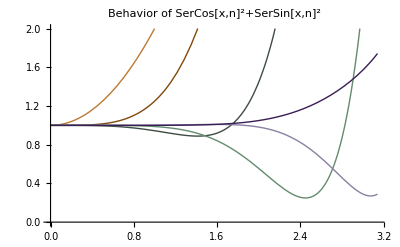

```mathematica
Plot[Evaluate[Table[Tooltip[SerCos[x,n]^2+SerSin[x,n]^2,StringForm["n=``",n]],{n,1,6}]],{x,0,π},PlotStyle->ColorData[41,"ColorList"],PlotRange->{0,2},PlotLabel->"Behavior of SerCos[x,n]^2+SerSin[x,n]^2"]
```

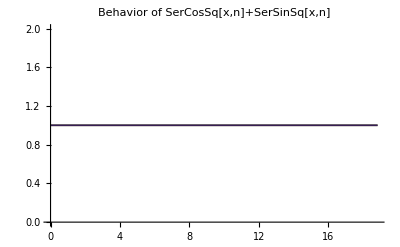

```mathematica
SerCosSq[x_,n_]:=Normal[Series[Cos[x]^2,{x,0,n}]];
SerSinSq[x_,n_]:=Normal[Series[Sin[x]^2,{x,0,n}]];
Plot[Evaluate[Table[Tooltip[SerCosSq[x,n]+SerSinSq[x,n],StringForm["n=``",n]],{n,1,6}]],{x,0,6π},PlotStyle->ColorData[41,"ColorList"],PlotRange->{0,2},PlotLabel->"Behavior of SerCosSq[x,n]+SerSinSq[x,n]"]
```

## Part 3

1.

```mathematica
Rx[θ_]:=({{1, 0, 0}, {0, Cos[θ], Sin[θ]}, {0, -Sin[θ], Cos[θ]}});
Ry[ζ_]:=({{Cos[ζ], 0, Sin[ζ]}, {0, 1, 0}, {-Sin[ζ], 0, Cos[ζ]}});
Rz[ϕ_]:=({{Cos[ϕ], Sin[ϕ], 0}, {-Sin[ϕ], Cos[ϕ], 0}, {0, 0, 1}});
```

2.

```mathematica
Rot3[ψ_,θ_,ϕ_]:=Rz[ψ].Rx[θ].Rz[ϕ];
FullSimplify[Rot3[ψ,θ,ϕ]]//MatrixForm
```

(Cos[ϕ] Cos[ψ]-Cos[θ] Sin[ϕ] Sin[ψ] | Cos[ψ] Sin[ϕ]+Cos[θ] Cos[ϕ] Sin[ψ] | Sin[θ] Sin[ψ]
-Cos[θ] Cos[ψ] Sin[ϕ]-Cos[ϕ] Sin[ψ] | Cos[θ] Cos[ϕ] Cos[ψ]-Sin[ϕ] Sin[ψ] | Cos[ψ] Sin[θ]
Sin[θ] Sin[ϕ] | -Cos[ϕ] Sin[θ] | Cos[θ])

3.

```mathematica
Rot3Inverse[ψ_,θ_,ϕ_]:=Rz[-ϕ].Rx[-θ].Rz[-ψ];
Simplify[Rot3Inverse[ψ,θ,ϕ].Rot3[ψ,θ,ϕ]]//MatrixForm
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

4.

```mathematica
Simplify[Inverse[Rot3[ψ,θ,ϕ]].Rot3[ψ,θ,ϕ]]//MatrixForm
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

Showing that difference between two inverses are same

```mathematica
Simplify[Inverse[Rot3[ψ,θ,ϕ]]-Rot3Inverse[ψ,θ,ϕ]//MatrixForm]
```

(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)